# Stability to Perturbation

Since our model is stable to perturbation as proven by the eigenvalues of the Jacobian, we would like to visualize this perturbation. We can do this by starting at the W state and doubling FS at the 400 minute mark and see how the system responds.

```mathematica
SetDirectory[NotebookDirectory[]];
FCL={20,10,5};
CIAL={80,70,68};
F2L={200,30,20};
F3L={3400,420,60};
FML={100,200,50};
FSL={500,150,300};
MPL={50,8500,20};
O2L={1.0,0.481333,1.22222};

(* Helper function to get easy access to list entry *)
at[list_, index_]:= list[[index]]
nestedAt[list_, index_, index2_]:=at[at[list, index], index2]

RegFunction[k_, n_, SP_, C_, x_]:=k/(1+Exp[n*(x-SP)])+C
getk23[list_]:=Module[{fccase,ciacase,f2case,f3case},fccase=RegFunction[0.293708,-0.248768,15.105,0,FC[t]];
ciacase=RegFunction[0.227484,-0.652642,71.4237,0,CIA[t]];
f2case=RegFunction[0.226644,-0.130635,37.073,0,F2[t]];
f3case=RegFunction[0.226655,-0.00362872,674.652,0,F3[t]];
Switch[list,FCL,fccase,CIAL,ciacase,F2L,f2case,F3L,f3case]]
getkO2[list_]:=Module[{fscase},fscase=RegFunction[95.3616,-0.0134783,258.284,0,FS[t]];
Switch[list,FSL,fscase]]
getkCIA[list_]:=Module[{o2case,fmcase,mpcase},o2case=RegFunction[4.661,-8.87757,1.41475,0.418826,O2[t]];
fmcase=RegFunction[5.50768,0.0387998,0.991932,0.41756,FM[t]];
mpcase=RegFunction[3.006,0.0690787,3.09565,0.42,MP[t]];
Switch[list,O2L,o2case,FML,fmcase,MPL,mpcase]]
getkCYT[list_]:=Module[{f2case,ciacase,f3case,fccase},f2case=RegFunction[16.6101,0.159447,7.90727,2.62995,F2[t]];
ciacase=RegFunction[1557.4,0.744197,59.1271,2.62967,CIA[t]];
f3case=RegFunction[5.00448,0.00537466,0.991933,2.62995,F3[t]];
fccase=RegFunction[2.15854,1.00162,8.74028,2.62992,FC[t]];
Switch[list,F2L,f2case,CIAL,ciacase,F3L,f3case,FCL,fccase]]
getkMIT[list_]:=Module[{fscase},fscase=RegFunction[168.632,0.022031,0.991933,0.538779,FS[t]];
Switch[list,FSL,fscase]]
getkMP[list_]:=Module[{o2case,mpcase,fmcase},o2case=RegFunction[4.1828,8.89003,0.130172,0,O2[t]];
mpcase=RegFunction[0.176593,-0.0142367,376.877,0,MP[t]];
fmcase=RegFunction[0.931282,-0.0587368,224.854,0.00105854,FM[t]];
Switch[list,O2L,o2case,MPL,mpcase,FML,fmcase]]
getkVAC[list_]:=Module[{f2case,ciacase,f3case,fccase},f2case=RegFunction[2.99975,-0.076787,56.8973,0,F2[t]];
ciacase=RegFunction[3.67913,-0.377767,76.0689,0,CIA[t]];
f3case=RegFunction[3.04175,-0.00213037,1396.83,0,F3[t]];
fccase=RegFunction[2.88787,-0.679725,14.0134,0.160357,FC[t]];
Switch[list,F2L,f2case,CIAL,ciacase,F3L,f3case,FCL,fccase]]
cases ={{FCL,FML,FCL,FSL,FCL,FSL,FML},{FCL,FML,FCL,FSL,FCL,FSL,MPL},{FCL,FML,FCL,FSL,F2L,FSL,FML},{FCL,FML,FCL,FSL,F2L,FSL,MPL},{FCL,FML,FCL,FSL,F3L,FSL,FML},{FCL,FML,FCL,FSL,F3L,FSL,MPL},{FCL,FML,CIAL,FSL,FCL,FSL,FML},{FCL,FML,CIAL,FSL,FCL,FSL,MPL},{FCL,FML,CIAL,FSL,F3L,FSL,FML},{FCL,FML,CIAL,FSL,F3L,FSL,MPL},{FCL,FML,F3L,FSL,F3L,FSL,FML},{FCL,FML,F3L,FSL,F3L,FSL,MPL},{FCL,MPL,FCL,FSL,FCL,FSL,FML},{FCL,MPL,FCL,FSL,FCL,FSL,MPL},{FCL,MPL,FCL,FSL,CIAL,FSL,FML},{FCL,MPL,FCL,FSL,F2L,FSL,FML},{FCL,MPL,FCL,FSL,F2L,FSL,MPL},{FCL,MPL,FCL,FSL,F3L,FSL,FML},{FCL,MPL,FCL,FSL,F3L,FSL,MPL},{FCL,MPL,CIAL,FSL,FCL,FSL,MPL},{FCL,MPL,CIAL,FSL,F3L,FSL,MPL},{FCL,MPL,F3L,FSL,F3L,FSL,FML},{FCL,MPL,F3L,FSL,F3L,FSL,MPL},{FCL,O2L,FCL,FSL,FCL,FSL,FML},{FCL,O2L,FCL,FSL,FCL,FSL,MPL},{FCL,O2L,FCL,FSL,CIAL,FSL,FML},{FCL,O2L,FCL,FSL,CIAL,FSL,MPL},{FCL,O2L,FCL,FSL,F2L,FSL,FML},{FCL,O2L,FCL,FSL,F2L,FSL,MPL},{FCL,O2L,FCL,FSL,F3L,FSL,FML},{FCL,O2L,FCL,FSL,F3L,FSL,MPL},{FCL,O2L,F3L,FSL,F3L,FSL,FML},{FCL,O2L,F3L,FSL,F3L,FSL,MPL},{CIAL,FML,FCL,FSL,FCL,FSL,FML},{CIAL,FML,FCL,FSL,FCL,FSL,MPL},{CIAL,FML,FCL,FSL,F3L,FSL,FML},{CIAL,FML,FCL,FSL,F3L,FSL,MPL},{CIAL,FML,CIAL,FSL,FCL,FSL,FML},{CIAL,FML,CIAL,FSL,FCL,FSL,MPL},{CIAL,FML,CIAL,FSL,F3L,FSL,FML},{CIAL,FML,CIAL,FSL,F3L,FSL,MPL},{CIAL,FML,F3L,FSL,FCL,FSL,FML},{CIAL,FML,F3L,FSL,FCL,FSL,MPL},{CIAL,FML,F3L,FSL,F3L,FSL,FML},{CIAL,FML,F3L,FSL,F3L,FSL,MPL},{CIAL,MPL,FCL,FSL,FCL,FSL,FML},{CIAL,MPL,FCL,FSL,FCL,FSL,MPL},{CIAL,MPL,FCL,FSL,CIAL,FSL,FML},{CIAL,MPL,FCL,FSL,F3L,FSL,FML},{CIAL,MPL,FCL,FSL,F3L,FSL,MPL},{CIAL,MPL,CIAL,FSL,FCL,FSL,MPL},{CIAL,MPL,CIAL,FSL,F3L,FSL,MPL},{CIAL,MPL,F3L,FSL,FCL,FSL,FML},{CIAL,MPL,F3L,FSL,FCL,FSL,MPL},{CIAL,MPL,F3L,FSL,F3L,FSL,FML},{CIAL,MPL,F3L,FSL,F3L,FSL,MPL},{CIAL,O2L,FCL,FSL,FCL,FSL,FML},{CIAL,O2L,FCL,FSL,FCL,FSL,MPL},{CIAL,O2L,FCL,FSL,CIAL,FSL,FML},{CIAL,O2L,FCL,FSL,CIAL,FSL,MPL},{CIAL,O2L,FCL,FSL,F3L,FSL,FML},{CIAL,O2L,FCL,FSL,F3L,FSL,MPL},{CIAL,O2L,F3L,FSL,FCL,FSL,FML},{CIAL,O2L,F3L,FSL,FCL,FSL,MPL},{CIAL,O2L,F3L,FSL,F3L,FSL,FML},{CIAL,O2L,F3L,FSL,F3L,FSL,MPL},{F2L,FML,FCL,FSL,FCL,FSL,FML},{F2L,FML,FCL,FSL,FCL,FSL,MPL},{F2L,FML,FCL,FSL,F2L,FSL,FML},{F2L,FML,FCL,FSL,F2L,FSL,MPL},{F2L,FML,FCL,FSL,F3L,FSL,FML},{F2L,FML,FCL,FSL,F3L,FSL,MPL},{F2L,FML,CIAL,FSL,FCL,FSL,FML},{F2L,FML,CIAL,FSL,FCL,FSL,MPL},{F2L,FML,CIAL,FSL,F2L,FSL,FML},{F2L,FML,CIAL,FSL,F2L,FSL,MPL},{F2L,FML,CIAL,FSL,F3L,FSL,FML},{F2L,FML,CIAL,FSL,F3L,FSL,MPL},{F2L,FML,F2L,FSL,FCL,FSL,FML},{F2L,FML,F2L,FSL,FCL,FSL,MPL},{F2L,FML,F2L,FSL,F2L,FSL,FML},{F2L,FML,F2L,FSL,F2L,FSL,MPL},{F2L,FML,F2L,FSL,F3L,FSL,FML},{F2L,FML,F2L,FSL,F3L,FSL,MPL},{F2L,FML,F3L,FSL,F2L,FSL,MPL},{F2L,FML,F3L,FSL,F3L,FSL,MPL},{F2L,MPL,FCL,FSL,FCL,FSL,FML},{F2L,MPL,FCL,FSL,FCL,FSL,MPL},{F2L,MPL,FCL,FSL,CIAL,FSL,FML},{F2L,MPL,FCL,FSL,F2L,FSL,FML},{F2L,MPL,FCL,FSL,F2L,FSL,MPL},{F2L,MPL,FCL,FSL,F3L,FSL,FML},{F2L,MPL,FCL,FSL,F3L,FSL,MPL},{F2L,MPL,CIAL,FSL,FCL,FSL,MPL},{F2L,MPL,CIAL,FSL,F3L,FSL,MPL},{F2L,MPL,F2L,FSL,FCL,FSL,FML},{F2L,MPL,F2L,FSL,FCL,FSL,MPL},{F2L,MPL,F2L,FSL,CIAL,FSL,FML},{F2L,MPL,F2L,FSL,F2L,FSL,FML},{F2L,MPL,F2L,FSL,F2L,FSL,MPL},{F2L,MPL,F2L,FSL,F3L,FSL,FML},{F2L,MPL,F2L,FSL,F3L,FSL,MPL},{F2L,MPL,F3L,FSL,F2L,FSL,MPL},{F2L,MPL,F3L,FSL,F3L,FSL,MPL},{F2L,O2L,FCL,FSL,FCL,FSL,FML},{F2L,O2L,FCL,FSL,FCL,FSL,MPL},{F2L,O2L,FCL,FSL,CIAL,FSL,FML},{F2L,O2L,FCL,FSL,CIAL,FSL,MPL},{F2L,O2L,FCL,FSL,F2L,FSL,FML},{F2L,O2L,FCL,FSL,F2L,FSL,MPL},{F2L,O2L,FCL,FSL,F3L,FSL,FML},{F2L,O2L,FCL,FSL,F3L,FSL,MPL},{F2L,O2L,F2L,FSL,FCL,FSL,FML},{F2L,O2L,F2L,FSL,FCL,FSL,MPL},{F2L,O2L,F2L,FSL,CIAL,FSL,FML},{F2L,O2L,F2L,FSL,CIAL,FSL,MPL},{F2L,O2L,F2L,FSL,F2L,FSL,FML},{F2L,O2L,F2L,FSL,F2L,FSL,MPL},{F2L,O2L,F2L,FSL,F3L,FSL,FML},{F2L,O2L,F2L,FSL,F3L,FSL,MPL},{F2L,O2L,F3L,FSL,F2L,FSL,MPL},{F2L,O2L,F3L,FSL,F3L,FSL,MPL},{F3L,FML,FCL,FSL,FCL,FSL,FML},{F3L,FML,FCL,FSL,FCL,FSL,MPL},{F3L,FML,FCL,FSL,F3L,FSL,FML},{F3L,FML,FCL,FSL,F3L,FSL,MPL},{F3L,FML,CIAL,FSL,FCL,FSL,FML},{F3L,FML,CIAL,FSL,FCL,FSL,MPL},{F3L,FML,CIAL,FSL,F3L,FSL,FML},{F3L,FML,CIAL,FSL,F3L,FSL,MPL},{F3L,FML,F3L,FSL,F3L,FSL,MPL},{F3L,MPL,FCL,FSL,FCL,FSL,FML},{F3L,MPL,FCL,FSL,FCL,FSL,MPL},{F3L,MPL,FCL,FSL,CIAL,FSL,FML},{F3L,MPL,FCL,FSL,F3L,FSL,FML},{F3L,MPL,FCL,FSL,F3L,FSL,MPL},{F3L,MPL,CIAL,FSL,FCL,FSL,MPL},{F3L,MPL,CIAL,FSL,F3L,FSL,MPL},{F3L,MPL,F3L,FSL,F3L,FSL,MPL},{F3L,O2L,FCL,FSL,FCL,FSL,FML},{F3L,O2L,FCL,FSL,FCL,FSL,MPL},{F3L,O2L,FCL,FSL,CIAL,FSL,FML},{F3L,O2L,FCL,FSL,CIAL,FSL,MPL},{F3L,O2L,FCL,FSL,F3L,FSL,FML},{F3L,O2L,FCL,FSL,F3L,FSL,MPL},{F3L,O2L,F3L,FSL,F3L,FSL,MPL}};
```

```mathematica
getSubstitutionRule[list_, state_]:= Switch[list, FCL,{FC[t]-> FCL[[state]]},  MPL,{MP[t]-> MPL[[state]]},  F2L,{F2[t]-> F2L[[state]]},  CIAL,{CIA[t]-> CIAL[[state]]},  F3L,{F3[t]-> F3L[[state]]},FSL, {FS[t]-> FSL[[state]]}, FML, {FM[t]-> FML[[state]]}, O2L , {O2[t]-> O2L[[state]]} ]
simulatePerturbation[startStateValue_, caseId_, startIron_, startkisu_, perturbTime_,stopTime_, factor_,regulated_] := Module[{alpha, kisu, Kcyt, Kmit, Kvac, Kcia, Kisu, KresO2, KF2, O2SP, OXYGEN, CARBON, kres, k23, kcia, kvac, caseValue, IRON, kmit, kcyt, kO2, kmp, Rcyt, Rmit, Rvac, Rcia, Risu, Rmp, RO2, Rres, R23, fcyt, fmit, fvac, ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, eqns, s,s2,fcm, ciam, f2m, f3m, fmm, fsm, mpm, o2m,localcheck},
caseValue = caseId;
IRON = startIron;
kisu =startkisu; 
alpha = 0.000222188885555*kisu + 0.00185188888889;

Kcyt = 10;
Kmit = 20;
Kvac = 20;
Kcia = 20; 
Kisu = 100;
KresO2 = 1;
KF2 = 200; 
O2SP = 1; 
OXYGEN = 100; 
 CARBON = 100; 
kres =36.363636363636363636364;




k23 =If[regulated, getk23[nestedAt[cases, caseValue, 1]], getk23[nestedAt[cases, caseValue, 1]]/. getSubstitutionRule[nestedAt[cases, caseValue, 1], startStateValue]];
kcia = If[regulated, getkCIA[nestedAt[cases, caseValue, 2]], getkCIA[nestedAt[cases, caseValue, 2]]/. getSubstitutionRule[nestedAt[cases, caseValue, 2], startStateValue]];
kvac = If[regulated, getkVAC[nestedAt[cases, caseValue, 3]], getkVAC[nestedAt[cases, caseValue, 3]]/. getSubstitutionRule[nestedAt[cases, caseValue, 3], startStateValue]];
kmit = If[regulated, getkMIT[nestedAt[cases, caseValue, 4]], getkMIT[nestedAt[cases, caseValue, 4]]/. getSubstitutionRule[nestedAt[cases, caseValue, 4], startStateValue]];
kcyt =If[regulated, getkCYT[nestedAt[cases, caseValue, 5]], getkCYT[nestedAt[cases, caseValue, 5]]/. getSubstitutionRule[nestedAt[cases, caseValue, 5], startStateValue]];
kO2 =If[regulated, getkO2[nestedAt[cases, caseValue, 6]], getkO2[nestedAt[cases, caseValue, 6]]/. getSubstitutionRule[nestedAt[cases, caseValue, 6], startStateValue]];
kmp =If[regulated, getkMP[nestedAt[cases, caseValue, 7]], getkMP[nestedAt[cases, caseValue, 7]]/. getSubstitutionRule[nestedAt[cases, caseValue, 7], startStateValue]];
Rcyt = kcyt * IRON/(Kcyt + IRON);
Rmit = kmit * FC[t]/(Kmit + FC[t]);
Rvac = kvac * FC[t]/(Kvac + FC[t]);
Rcia = kcia * FC[t]/(Kcia+FC[t]);
Risu = kisu * FM[t]/(Kisu + FM[t])*O2SP/(O2SP+O2[t]);
Rmp = kmp * FM [t]* O2[t];
RO2 = kO2 * (OXYGEN- O2[t]); 
Rres = kres * FS[t] * O2[t]/(KresO2 + O2[t]);
R23 = k23 * F2[t] /(KF2+F2[t])*OXYGEN;
fcyt = 0.8;
fmit = 0.1;
fvac = 0.1; 
ode1=FC'[t]==Rcyt-Rvac-Rmit-Rcia-alpha*FC[t];
ode2=CIA'[t]==Rcia-alpha*CIA[t];
ode3=F2'[t]==fcyt/fvac*Rvac-R23-alpha*F2[t];
ode4=F3'[t]==R23-alpha*F3[t];
ode5=FM'[t]==fcyt/fmit*Rmit-Risu-Rmp-alpha*FM[t];
ode6=FS'[t]==Risu-alpha*FS[t];
ode7=MP'[t]==Rmp-alpha*MP[t];
ode8=O2'[t]==RO2-Rmp-Rres-alpha*O2[t];
eqns = {ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, FC[0] ==FCL[[startStateValue]], CIA[0]==CIAL[[startStateValue]], F2[0] == F2L[[startStateValue]], F3[0]==F3L[[startStateValue]], FM[0]==FML[[startStateValue]],MP[0]== MPL[[startStateValue]], FS[0]==FSL[[startStateValue]], O2[0]== O2L[[startStateValue]]};
s = NDSolve[eqns,{FC, CIA, F2, F3, FM, FS, MP, O2},{t, 0, perturbTime}];

perturbedEqns = {ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, FC[perturbTime] ==FCL[[startStateValue]], CIA[perturbTime]==CIAL[[startStateValue]], F2[perturbTime] == F2L[[startStateValue]], F3[perturbTime]==F3L[[startStateValue]], FM[perturbTime]==FML[[startStateValue]],MP[perturbTime]== MPL[[startStateValue]], FS[perturbTime]==factor*FSL[[startStateValue]], O2[perturbTime]== O2L[[startStateValue]]};

s2 = NDSolve[perturbedEqns, {FC, CIA, F2, F3, FM, FS, MP, O2},{t, perturbTime, stopTime}];
<<NumericalCalculus`;

FCD[t_?NumericQ] := Which[0 <= t <= perturbTime, (FC[t]/.s)[[1]], perturbTime < t <= stopTime, (FC[t]/.s2)[[1]]];
CIAD[t_?NumericQ] := Which[0 <= t <= perturbTime, CIA[t]/.s[[1]], perturbTime < t <= stopTime, CIA[t]/.s2[[1]]];
F2D[t_?NumericQ] := Which[0 <= t <= perturbTime, F2[t]/.s[[1]], perturbTime < t <= stopTime, F2[t]/.s2 [[1]]];
F3D[t_?NumericQ] := Which[0 <= t <= perturbTime, F3[t]/.s[[1]], perturbTime < t <= stopTime, F3[t]/.s2[[1]]];
FMD[t_?NumericQ] := Which[0 <= t <= perturbTime, FM[t]/.s[[1]], perturbTime < t <= stopTime, FM[t]/.s2[[1]]];
MPD[t_?NumericQ] := Which[0 <= t <= perturbTime, MP[t]/.s[[1]], perturbTime < t <= stopTime, MP[t]/.s2[[1]]];
FSD[t_?NumericQ] := Which[0 <= t <= perturbTime, FS[t]/.s[[1]], perturbTime < t <= stopTime, FS[t]/.s2[[1]]];
O2D[t_?NumericQ] := Which[0 <= t <= perturbTime, O2[t]/.s[[1]], perturbTime < t <= stopTime, O2[t]/.s2 [[1]]];

(*To normalize from 0 to 1 we must find the maximum*)
localcheck = stopTime;
fcm =NMaximize[{FCD[t], 0≤ t ≤ localcheck}, t, Method->"RandomSearch"] [[1]];
ciam =NMaximize[{CIAD[t], 0 ≤ t ≤ localcheck}, t, Method->"RandomSearch"][[1]];
f2m =NMaximize[{F2D[t], 0 ≤ t ≤ localcheck}, t, Method->"RandomSearch"][[1]];f3m =NMaximize[{F3D[t], 0≤ t ≤ localcheck}, t, Method->"RandomSearch"][[1]];fmm =NMaximize[{FMD[t], 0 ≤ t ≤ localcheck}, t, Method->"RandomSearch"][[1]];fsm =NMaximize[{FSD[t], 0 ≤ t ≤ localcheck}, t, Method->"RandomSearch"][[1]];mpm =NMaximize[{MPD[t], 0 ≤ t ≤ localcheck}, t, Method->"RandomSearch"][[1]];o2m =NMaximize[{O2D[t], 0 ≤ t ≤ localcheck}, t, Method->"RandomSearch"][[1]];
a = Plot[Rescale[Evaluate[MPD[t]],{0,mpm}], {t,0, stopTime}, PlotRange->{0,10000}, PlotStyle->{Blue}];
c = Plot[Rescale[Evaluate[FCD[t]],{0, fcm}], {t,0, stopTime}, PlotRange->{0,10000}, PlotStyle->{Red}];

d = Plot[Rescale[Evaluate[F2D[t]],{0, f2m}], {t,0, stopTime}, PlotRange->{0,10000}, PlotStyle->{RGBColor[0,0.5,0]}];e = Plot[Rescale[Evaluate[CIAD[t]],{0,ciam}], {t,0, stopTime}, PlotRange->{0,10000}, PlotStyle->{Orange}];f = Plot[Rescale[Evaluate[F3D[t]],{0, f3m}], {t,0, stopTime}, PlotRange->{0,10000}, PlotStyle->{Purple}];

g = Plot[Rescale[Evaluate[FSD[t]],{0, fsm}], {t,0, stopTime}, PlotRange->{0,10000}, PlotStyle->{Black}];
h = Plot[Rescale[Evaluate[FMD[t]],{0,fmm}], {t,0, stopTime}, PlotRange->{0,10000}, PlotStyle->{Cyan}];
i = Plot[Rescale[Evaluate[O2D[t]],{0,o2m}], {t,0, stopTime}, PlotRange->{0,10000}, PlotStyle->{Magenta}];
 Show[a,c,d,e,f,g,h,i, PlotRange->{ {0, stopTime},{0.3, 1.1}}, PlotLabel-> "",Axes->False,Frame->{{True,False},{True,False}},BaseStyle->{PrintPrecision->2} ]

]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

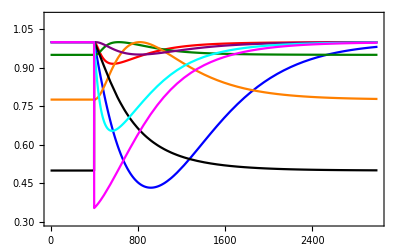

```mathematica
perturbRegulated = simulatePerturbation[1, 1, 40, 6.666, 400, 3000,2, True]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

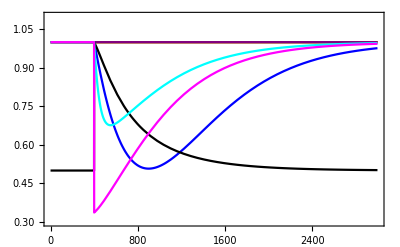

```mathematica
perturbNotRegulated = simulatePerturbation[1,1,40,6.666,400,3000,2, False]
```

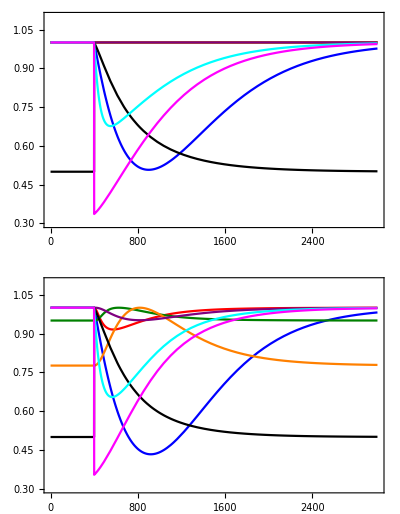
-Graphics-Time (minutes)Normalized Component Concentration

```mathematica
stackedGraphs = GraphicsColumn[{perturbNotRegulated, perturbRegulated}];
labeledFigure =Labeled[stackedGraphs, {"Time (minutes)", "Normalized Component Concentration"},{Bottom, Left}, RotateLabel->True];
perturbFigure =  Legended[labeledFigure,  LineLegend[{Blue, Red, RGBColor[0,0.5,0], Orange, Purple,  Black ,Cyan, Magenta}, {"MP","FC","F2","CIA","F3","FS","FM","O2"}]]
```